```mathematica
2*αH*(αH-r/2)-(αH-r/2)^2//FullSimplify
```

-r^2/4+αH^2

```mathematica
αL^2 - r^2/2/.{r->-1+αL + αH}//FullSimplify
```

```mathematica
?Maximize
```

System`Maximize

Attributes[Maximize]={Protected}
 
Options[Maximize]={WorkingPrecision→∞}

```mathematica
p=0.15
```

0.15

```mathematica
Maximize[{αL^2-1/2 (-1+αH+αL)^2, αH > αL , αL > 0 , αH > 0, αL < 1 , αH < 1, αH^2 > p, αL^2 < p},{αL,αH}]
```

{0.15,{αL→0.387298,αH→0.612705}}

```mathematica
?ContourPlot
```

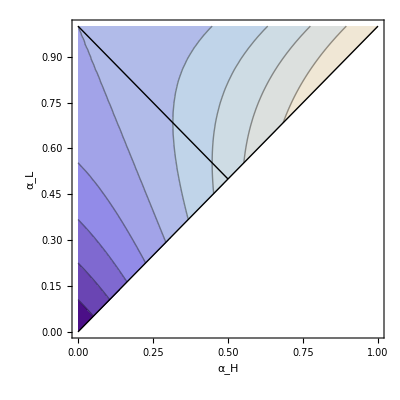

```mathematica
g = ContourPlot[If[αH>αL,αL^2-1/2 (-1+αH+αL)^2,Null],{αL,0,1},{αH,0,1}, AxesLabel->{"α_H","α_L"},Epilog->{Line[{{0,0},{1,1}}],
Line[{{1/2,1/2},{0,1}}] 
} ]
```

```mathematica
Export["../writeup/plots/welfare.pdf",g]
```

../writeup/plots/welfare.pdf

```mathematica
optimalPair[P_]:={αL,αH}/.Maximize[{αL^2-1/2 (-1+αH+αL)^2, αH > αL , αL > 0 , αH > 0, αL < 1 , αH < 1, αH^2 > P, αL^2 < P},{αL,αH}][[2]]
```

```mathematica
optimalPair[.14]
```

{0.374166,0.625836}

```mathematica
Manipulate[ContourPlot[If[αH>αL,αL^2-1/2 (-1+αH+αL)^2,Null],{αL,0,1},{αH,0,1}, AxesLabel->{"α_H","α_L"},Epilog->{
Line[{{0,0},{1,1}}],
Line[{{0,Sqrt[p]},{Sqrt[p],Sqrt[p]}}],
Line[{{Sqrt[p],0},{Sqrt[p],1}}],
{Red,Point[optimalPair[p]]}
} ],{{p,0.5},0,1}]
```

```mathematica
Plot3D[αL^2-1/2 (-1+αH+αL)^2,{αL,0,1},{αH,0,1}]
```

-Graphics3D-

```mathematica
D[αL^2-1/2 (-1+αH+αL)^2,αH]
```

1-αH-αL

```mathematica
Expand[αL^2-1/2 (-1+αH+αL)^2]
```

-1/2+αH-αH^2/2+αL-αH αL+αL^2/2

```mathematica
Collect[αL^2-1/2 (-1+αH+αL)^2,{αL,αH}]
```

-1/2+αH-αH^2/2+(1-αH) αL+αL^2/2

```mathematica
2*αL*(αL-r/2)-(αL-r/2)^2-r*(αL-r/2)//FullSimplify
```

```mathematica
1/4 (r-2 αL)^2/.{r->-1+αL + αH}//FullSimplify
```

1/4 (1-αH+αL)^2

```mathematica
2*αH*(αH-r/2)-(αH-r/2)^2+r*(αL-r/2)-αH^2//FullSimplify
```

```mathematica
-(3 r^2)/4+r αL/.{r->-1+αL + αH}//FullSimplify
```

1/4 (3-3 αH+αL) (-1+αH+αL)

```mathematica
-(3 r^2)/4+αH^2+r αL/.{r->-1+αL + αH}//FullSimplify
```

αH^2+αL (-1+αH+αL)-3/4 (-1+αH+αL)^2